Hard wall at x < 0, wall of height V0 up to x = aa

```mathematica
psi1[x_] := AA Sin[Sqrt[EE - V0] x]
```

```mathematica
psi2[x_] := Exp[-I Sqrt[EE] x] + RR Exp[I Sqrt[EE] x]
```

```mathematica
psi[x_] := If[x < aa,psi1[x],psi2[x]]
```

```mathematica
Solve[{
psi1[aa] == psi2[aa],
psi1'[aa] == psi2'[aa]},
{AA, RR}]
```

{{AA→(2 ⅇ^(-ⅈ aa √EE) √EE)/(ⅈ √(EE-V0) Cos[aa √(EE-V0)]+√EE Sin[aa √(EE-V0)]),RR→-ⅇ^(-2 ⅈ aa √EE)+(2 ⅇ^(-2 ⅈ aa √EE) √EE Sin[aa √(EE-V0)])/(ⅈ √(EE-V0) Cos[aa √(EE-V0)]+√EE Sin[aa √(EE-V0)])}}

```mathematica
RR := -ⅇ^(-2 ⅈ aa √EE)+(2 ⅇ^(-2 ⅈ aa √EE) √EE Sin[aa √(EE-V0)])/(ⅈ √(EE-V0) Cos[aa √(EE-V0)]+√EE Sin[aa √(EE-V0)])
AA := (2 ⅇ^(-ⅈ aa √EE) √EE)/(ⅈ √(EE-V0) Cos[aa √(EE-V0)]+√EE Sin[aa √(EE-V0)])
```

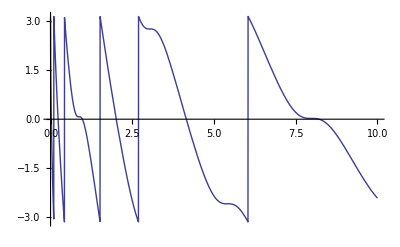

```mathematica
Plot[Arg[RR /. {V0 -> -10, aa -> 10}], {EE, 0, 10}]
```

```mathematica
V0 := -10
aa := 10
```

```mathematica
Plot3D[Norm[psi[x]]^2 , {EE, 0, 20}, {x, 0, 10}, ImageSize->Full, PlotPoints->50]
```

-Graphics3D-